```mathematica
Get[NotebookDirectory[]<>"LandslideProcessor.wl"]
data=Import[NotebookDirectory[]<>"data/LandslideFailureSurfaces.xlsx"];

(*Process all 15 sheets*)
processed=processSheet/@data[[1;;15]];

(*Extract important quantities*)
rescaledB=processed[[All,1]];
rescaledH=processed[[All,2]];
fits=processed[[All,3]];
b0vals = processed[[All,4]];
αvals = Abs[processed[[All,5]]];
αError = processed[[All,6]];
```

{0.322641,0.478352}

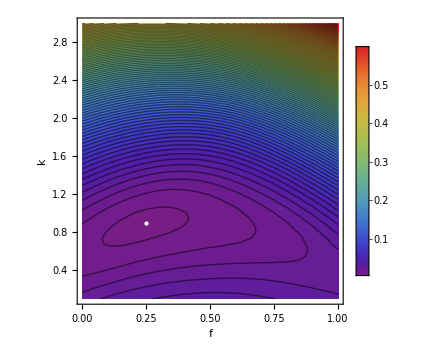

```mathematica
index = 3;
{b0vals[[index]],αvals[[index]]}
xhdata = rescaledH[[index]][[All,1]];
xbdata = rescaledB[[index]][[All,1]];
hdata = rescaledH[[index]][[All,2]];
bdata = rescaledB[[index]][[All,2]];

(*Modules to compute best-fit f,k values to fit x,h data*)
misfit[{f_?NumericQ,k_?NumericQ},α_,b0_,xdata_,hdata_]:=Module[{sol,Hfun,hmodel},
sol=HSolution[α,f,b0,k,{-1,1}];
If[sol===$Failed,Return[10^6]  (*big penalty if solver fails*)];
Hfun=sol[[1]];
(*interpolating function*)
hmodel[x_]:=Piecewise[{{Hfun[x],Hfun[x]>0}},0]+b0 (x^2-1);
Total[(hdata-hmodel/@xdata)^2]/(Length[xdata]-2)
]

(*Define ranges for f and k*)
fvals=Range[0,1,0.05];
kvals=Range[0.1,3,0.05];

(*Compute misfit over the grid*)
misfitGrid=Table[misfit[{f,k},αvals[[index]],b0vals[[index]],xhdata,hdata],{k,kvals},{f,fvals}];
(*Minimum value*)
minValue=Min[misfitGrid];
(*Position (row,column) of the minimum*)
minPos=Position[misfitGrid,minValue][[1]];
kval=kvals[[minPos[[1]]]];
fval=fvals[[minPos[[2]]]];

(*Density plot*)
p1=ListDensityPlot[misfitGrid,DataRange->{{Min[fvals],Max[fvals]},{Min[kvals],Max[kvals]}},FrameLabel->{"f","k"},ColorFunction->"Rainbow",PlotLegends->Automatic];

(*Contour plot*)
p2=ListContourPlot[misfitGrid,DataRange->{{Min[fvals],Max[fvals]},{Min[kvals],Max[kvals]}},FrameLabel->{"f","k"},Contours->100,ColorFunction->"Rainbow",PlotLegends->Automatic];

Show[p1,p2,Graphics[{White,PointSize[Large],Point[{fval,kval}]}],ImageSize->Medium]
```

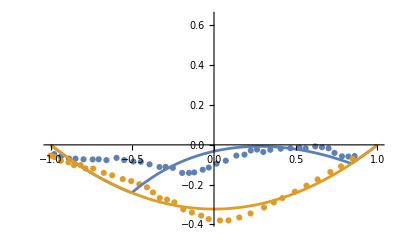

```mathematica
Hsol=HSolution[αvals[[index]],fval,b0vals[[index]],kval,{-1,1}];
H=Hsol[[1]] ;
hmodel[x_]:=Piecewise[{{H[x],H[x]>0}},0]+b0vals[[index]] (x^2-1);
p1=ListPlot[{Transpose[{xhdata,hdata}],Transpose[{xbdata,bdata}]},PlotRange->Full];
p2=Plot[{hmodel[x],
b0vals[[index]]*(x^2-1)},
{x,-1,1},ImageSize->Large];
Show[p1,p2,PlotRange->{-b0vals[[index]]*1.2,2*b0vals[[index]]}]
```

```mathematica
(*Assuming b0vals and αvals are already defined for all landslides*)resultsAll=Table[Module[{xhdata,xbdata,hdata,bdata,misfitGrid,minValue,minPos,fval,kval,
indicesInThreshold,fInThreshold,kInThreshold,fUncertainty,kUncertainty},(*Extract data for current landslide index*)
xhdata=rescaledH[[index]][[All,1]];
xbdata=rescaledB[[index]][[All,1]];
hdata=rescaledH[[index]][[All,2]];
bdata=rescaledB[[index]][[All,2]];
(*Compute misfit over grid*)misfitGrid=Table[misfit[{f,k},αvals[[index]],b0vals[[index]],xhdata,hdata],{k,kvals},{f,fvals}];
(*Find minimum and corresponding f,k*)
minValue=Min[misfitGrid];
minPos=Position[misfitGrid,minValue][[1]];
kval=kvals[[minPos[[1]]]];
fval=fvals[[minPos[[2]]]];
(*uncertainty bounds*)
indicesInThreshold=Position[misfitGrid,x_/;x<=1.2*minValue];
fInThreshold=fvals[[indicesInThreshold[[All,2]]]];kInThreshold=kvals[[indicesInThreshold[[All,1]]]];
fUncertainty=Abs[Min[fInThreshold]-Max[fInThreshold]]/2;kUncertainty=Abs[Min[kInThreshold]-Max[kInThreshold]]/2;
(*Return results for this landslide*)
{b0vals[[index]],kval,kUncertainty,αvals[[index]],αError[[index]],fval,fUncertainty}],{index,1,Length[rescaledH]}];

resultsAll//TableForm
```

0.297928 | 0.95 | 0.125 | 0.635028 | 0.0213216 | 0.65 | 0.15
0.259864 | 0.9 | 0.15 | 0.480936 | 0.0173195 | 0.5 | 0.175
0.322641 | 0.9 | 0.125 | 0.478352 | 0.022396 | 0.25 | 0.1
0.125534 | 1.45 | 0.05 | 0.113867 | 0.0154596 | 0.15 | 0.
0.288696 | 1.3 | 0.175 | 0.45979 | 0.0311235 | 0.55 | 0.125
0.199804 | 1.2 | 0.15 | 0.267325 | 0.0171355 | 0.35 | 0.075
0.197273 | 1.6 | 0.1 | 0.625753 | 0.0202158 | 0.65 | 0.05
0.145285 | 1.75 | 0.2 | 0.69286 | 0.0176363 | 0.7 | 0.05
0.0354612 | 2.55 | 0.15 | 0.11463 | 0.00634255 | 0.1 | 0.
0.129438 | 1.4 | 0.1 | 0.184747 | 0.013312 | 0.15 | 0.025
0.100853 | 1.4 | 0.15 | 0.111685 | 0.008615 | 0.1 | 0.
0.55577 | 0.8 | 0.05 | 0.458843 | 0.0429706 | 0.55 | 0.15
0.346355 | 1.05 | 0.1 | 0.627232 | 0.0318313 | 0.45 | 0.1
0.131599 | 1.75 | 0.075 | 0.640536 | 0.015466 | 0.65 | 0.025
0.219055 | 1.65 | 0.05 | 0.220304 | 0.0271464 | 0.25 | 0.

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/ResultsLandslideDatabase.csv

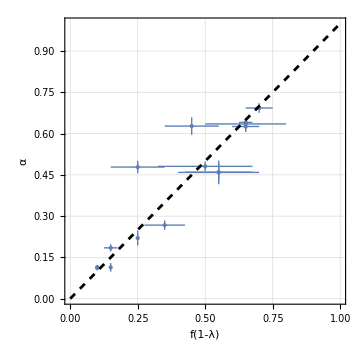

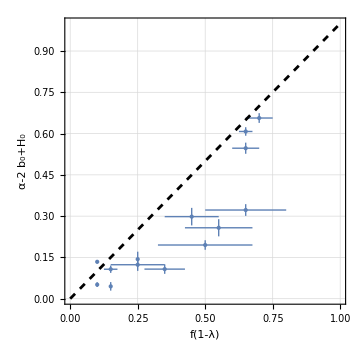

```mathematica
fvals = resultsAll[[All,6]];
fUnc = resultsAll[[All,7]];
kvals=resultsAll[[All,2]];

pts=Transpose[{fvals,αvals,fUnc,αError}];
(*Attach error bars*)
pointsWithErrors=pts/. {f_,α_,Δf_,Δα_}:>{Around[f,Δf],Around[α,Δα]};
p2=ListPlot[pointsWithErrors,Frame->True,FrameLabel->{Style["f(1-λ)",18],Style["α",18]},PlotStyle->{DarkBlue,PointSize[Medium]},PlotRange->All,GridLines->Automatic,PlotTheme->"Detailed"];

pts=Transpose[{fvals,αvals-(2-kvals)*b0vals,fUnc,αError}];
(*Export data to text file*)
header={"f","α","ϵf","ϵα"};
dataWithHeader=Prepend[pts,header];
Export[NotebookDirectory[]<>"ResultsLandslideDatabase.csv",dataWithHeader,"CSV"]

pointsWithErrors=pts/. {f_,α_,Δf_,Δα_}:>{Around[f,Δf],Around[α,Δα]};
p3=ListPlot[pointsWithErrors,Frame->True,FrameLabel->{Style["f(1-λ)",18],Style["α"+Subscript["H",0]-2 Subscript["b",0],18]},PlotStyle->{DarkBlue,PointSize[Medium]},PlotRange->All,GridLines->Automatic,PlotTheme->"Detailed"];

p4=Plot[x,{x,0,1},PlotStyle->{Black,Dashed}];
Show[p2,p4,AspectRatio->1,PlotRange->{{0,1},{0,1}},FrameTicksStyle->Directive[FontSize->18],Frame->True,ImageSize->Medium]
Show[p3,p4,AspectRatio->1,PlotRange->{{0,1},{0,1}},FrameTicksStyle->Directive[FontSize->18],Frame->True,ImageSize->Medium]
```